```mathematica
points=ToExpression[Import["/home/tatjam/code/tfg/workdir/wing.dat","String"]];
```

```mathematica
normals=ToExpression[Import["/home/tatjam/code/tfg/workdir/wing_nrm.dat","String"]];
```

```mathematica
Graphics3D[{Thick,Red,Arrow[{{0,0,0},{0,0,1}}] (*Towards leading edge*),White, Polygon[points[[]]],Black,Arrowheads[Small],normals}]
```

-Graphics3D-

```mathematica
mat=Import["/home/tatjam/code/tfg/workdir/mat.dat"];
```

```mathematica
ArrayPlot[mat,PlotLegends->Automatic]
```

-Graphics-

```mathematica
dynmat=Import["/home/tatjam/code/tfg/workdir/dyn_mat.dat"];
```

```mathematica
ArrayPlot[dynmat,PlotLegends->Automatic]
```

-Graphics-

```mathematica
sln=Import["/home/tatjam/code/tfg/workdir/sln.dat"][[1]];
wake=ToExpression[Import["/home/tatjam/code/tfg/workdir/wake.dat","String"]];
wakesln=Import["/home/tatjam/code/tfg/workdir/wake_sln.dat"][[1]];
```

```mathematica
maxsol=Max[Abs[sln]];
```

```mathematica
If[maxsol==0,maxsol=0.0001];
```

```mathematica
maxwakesol=Max[Abs[wakesln]];
```

```mathematica
If[maxwakesol==0,maxwakesol=0.0001];
```

```mathematica
colorEach[p_,c_]:={FaceForm[ColorData["GrayYellowTones"][Abs[c/maxwakesol]]],Polygon[p]}
```

```mathematica
colorEachWake[p_,c_]:={FaceForm[ColorData["TemperatureMap"][Abs[c/maxwakesol]]],Polygon[p]}
```

```mathematica
Legended[Graphics3D[
ArrayFlatten[{EdgeForm[None],MapThread[colorEach,{points, sln}],MapThread[colorEachWake,{wake, wakesln}]},1],Lighting->{{"Ambient", White}}],{BarLegend[{"GrayYellowTones",{0,maxwakesol}}],BarLegend[{"TemperatureMap",{0,maxwakesol} }]}]
```

-Graphics3D-

```mathematica
cps=Import["/home/tatjam/code/tfg/workdir/cps.dat"][[1]];
```

```mathematica
maxcp=Max[cps]
```

0.0541497

```mathematica
mincp=Min[cps]
```

-1.52502

```mathematica
If[maxcp==0,maxcp=0.0001];
```

```mathematica
colorEachCp[p_,c_]:={EdgeForm[None],FaceForm[ColorData["Rainbow"][(c-mincp)/(maxcp-mincp)]],Polygon[p]}
```

```mathematica
Legended[Graphics3D[
ArrayFlatten[{MapThread[colorEachCp,{points, cps}](*,Polygon[wake]*)},1],Lighting->{{"Ambient", White}}],BarLegend[{"Rainbow",{mincp,maxcp}}]]
```

-Graphics3D-

```mathematica
liftTime=Import["/home/tatjam/code/tfg/workdir/lift_over_time.dat"][[1]];
liftTimeSteady=Import["/home/tatjam/code/tfg/workdir/lift_over_time_steady.dat"][[1]];
```

La idea es calcular el lift estacionario para obtener el factor de correción de forma
y con ello normalizar los lift al de Theodorsen y compararlos.
¿¿¿Porqué leches va el phase shift del revés???

```mathematica
finalLift=liftTimeSteady[[-1]];
```

```mathematica
0.0625*1/0.25
```

0.25

```mathematica
ts=Table[0.0625*i, {i, 0,99}];
heaveampl=0.1;
ω=2.0;
AoA=heaveampl*Sin[ω*ts];
vel=1.0;
chord=0.25;
tadim=ts*vel/chord;
```

```mathematica
k=(2*0.25)/(2*1.0);
```

```mathematica
besselH0[k_]:=BesselJ[0,k]-I*BesselY[0,k];
```

```mathematica
besselH1[k_]:=BesselJ[1,k]-I*BesselY[1,k];
```

```mathematica
theodorsenLag[k_]=besselH1[k]/(besselH1[k]+I*besselH0[k]);
```

```mathematica
Arg[theodorsenLag[k]]*180/π
```

-14.9752

```mathematica
hampl=vel* heaveampl/ω;
hampl
```

0.05

```mathematica
clQ:=2π*AoA;
clA:=2π*(-k*k*hampl/chord)*Exp[I*ω*ts]
```

```mathematica
cls:=Re[theodorsenLag[k]*clQ+clA];
```

```mathematica
dataWithTime[data_,time_]:=
Thread[{#2,#1}&[data,time]]
```

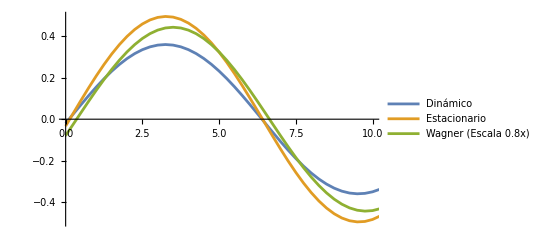

```mathematica
ListLinePlot[{
dataWithTime[liftTime/chord,tadim],
dataWithTime[liftTimeSteady/chord,tadim],
dataWithTime[cls,tadim]},
PlotLegends->{"Dinámico", "Estacionario","Wagner (Escala 0.8x)"},PlotRange->{{0,10},All}]
```

```mathematica
datos=ToExpression[Import["/home/tatjam/code/tfg/workdir/flowmap.dat", "String"]];
```

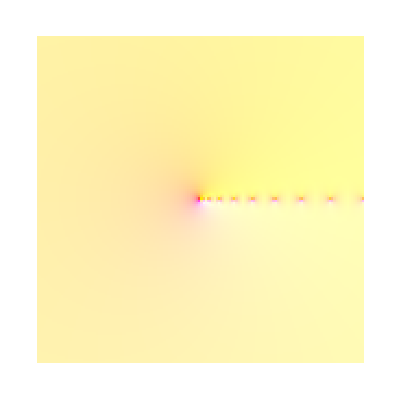

```mathematica
ArrayPlot[datos]
```